This notebook is associated with the paper “Quantum hypothesis testing in many-body systems” by Jan de Boer, Victor Godet, Jani Kastikainen and Esko Keski-Vakkuri (arxiv.org/abs/2007.11711).

It implements measurements of a qubit in the context of (asymmetric) quantum hypothesis testing. The measurement is applied to N copies of the system and optimized to distinguish between two given states of the qubit.

This notebook contains an implementation of the optimal measurement and of a suboptimal but simpler measurement: the likelihood ratio test (which can also be performed with the quantum circuit given in Figure 5). These two measurements are compared and plots (given in Figure 6) are generated. 

We also compute the various information quantities (the relative entropy and the relative entropy variance) appearing in these measurements.

## Quantum hypothesis testing for a qubit

### Setup

We define the two states ρ and σ of the qubit.

```mathematica
$Assumptions=And[E0>0,E1>0,E0>E1,θ>-π,θ<π,p>0,p<1/2];

Rot={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
σ=({{ⅇ^-E0, 0}, {0, ⅇ^-E1}});
ρ=Transpose[Rot].σ.Rot//Simplify;

Etop={E0->-Log[p],E1->-Log[1-p]};
```

```mathematica
ρ//MatrixForm
```

(ⅇ^-E0 Cos[θ]^2+ⅇ^-E1 Sin[θ]^2 | (-ⅇ^-E0+ⅇ^-E1) Cos[θ] Sin[θ]
(-ⅇ^-E0+ⅇ^-E1) Cos[θ] Sin[θ] | ⅇ^-E1 Cos[θ]^2+ⅇ^-E0 Sin[θ]^2)

### Information quantities

We compute the information quantities which appear in the measurement protocols: the relative entropy and the relative entropy variance.

```mathematica
Sρ=-Tr[ρ.MatrixLog[ρ]]//Simplify
```

ⅇ^-E0 E0+ⅇ^-E1 E1

```mathematica
Sρσ=Tr[ρ.MatrixLog[ρ]]-Tr[ρ.MatrixLog[σ]]//FullSimplify
```

ⅇ^(-E0-E1) (ⅇ^E0-ⅇ^E1) (E0-E1) Sin[θ]^2

```mathematica
Sρσ/.Etop//Simplify
```

-(-1+2 p) Log[-1+1/p] Sin[θ]^2

```mathematica
Vρσ=Tr[ρ.(MatrixLog[ρ]-MatrixLog[σ]).(MatrixLog[ρ]-MatrixLog[σ])]-Sρσ^2//Simplify
```

1/2 ⅇ^(-2 (E0+E1)) (E0-E1)^2 (-ⅇ^(2 E0)-ⅇ^(2 E1)+2 ⅇ^(E0+E1)+2 ⅇ^(2 E0+E1)+2 ⅇ^(E0+2 E1)+(ⅇ^E0-ⅇ^E1)^2 Cos[2 θ]) Sin[θ]^2

```mathematica
Vρσ/.Etop//Simplify
```

1/2 (1+4 p-4 p^2+(1-2 p)^2 Cos[2 θ]) Log[-1+1/p]^2 Sin[θ]^2

#### Perturbative ratio

We plot the perturbative ratio V/S, for which a lower bound is proven in section 3.2

```mathematica
S2ρσ=Series[Sρσ/.Etop,{θ,0,2}]
```

-(-1+2 p) (Log[1-p]-Log[p]) θ^2+O[θ]^3

```mathematica
V2ρσ=Series[Vρσ/.Etop,{θ,0,2}]
```

(Log[1-p]-Log[p])^2 θ^2+O[θ]^3

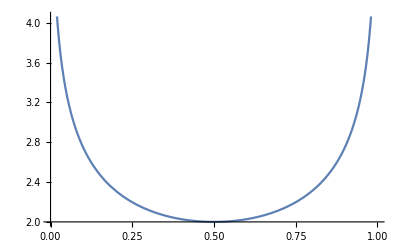

```mathematica
Plot[Normal[V2ρσ/S2ρσ],{p,0,1}]
```

Consistently with our lower bound, the ratio is larger than two, with equality when the two density matrices commute.

#### Diagonal part

We also compute information quantities involving the diagonal part of ρ, denoted ρD. These appear in the likelihood ratio test.

```mathematica
ρD={{ρ[[1,1]],0},{0,ρ[[2,2]]}}
```

{{ⅇ^-E0 Cos[θ]^2+ⅇ^-E1 Sin[θ]^2,0},{0,ⅇ^-E1 Cos[θ]^2+ⅇ^-E0 Sin[θ]^2}}

```mathematica
SρDσ=Tr[ρD.MatrixLog[ρD]]-Tr[ρD.MatrixLog[σ]]//Simplify
```

ⅇ^(-E0-E1) (Cos[θ]^2 (ⅇ^E1 E0+ⅇ^E0 E1+ⅇ^E0 Log[ⅇ^-E1 Cos[θ]^2+ⅇ^-E0 Sin[θ]^2]+ⅇ^E1 Log[ⅇ^-E0 Cos[θ]^2+ⅇ^-E1 Sin[θ]^2])+(ⅇ^E0 E0+ⅇ^E1 E1+ⅇ^E1 Log[ⅇ^-E1 Cos[θ]^2+ⅇ^-E0 Sin[θ]^2]+ⅇ^E0 Log[ⅇ^-E0 Cos[θ]^2+ⅇ^-E1 Sin[θ]^2]) Sin[θ]^2)

```mathematica
SρDσ/.Etop//FullSimplify
```

1/2 ((-1+2 p) Cos[2 θ] Log[((-1+p) (1+(-1+2 p) Cos[2 θ]))/(p (-1+(-1+2 p) Cos[2 θ]))]-Log[(4 (-1+p) p)/(-1+(1-2 p)^2 Cos[2 θ]^2)])

```mathematica
VρDσ=Tr[ρD.(MatrixLog[ρD]-MatrixLog[σ]).(MatrixLog[ρD]-MatrixLog[σ])]-SρDσ^2//Simplify
```

ⅇ^(-2 (E0+E1)) (ⅇ^(E0+E1) Log[ⅇ^E1/(ⅇ^E1 Cos[θ]^2+ⅇ^E0 Sin[θ]^2)]^2 (ⅇ^E1 Cos[θ]^2+ⅇ^E0 Sin[θ]^2)+ⅇ^(E0+E1) Log[ⅇ^E0/(ⅇ^E0 Cos[θ]^2+ⅇ^E1 Sin[θ]^2)]^2 (ⅇ^E0 Cos[θ]^2+ⅇ^E1 Sin[θ]^2)-(Cos[θ]^2 (ⅇ^E1 E0+ⅇ^E0 E1+ⅇ^E0 Log[ⅇ^-E1 Cos[θ]^2+ⅇ^-E0 Sin[θ]^2]+ⅇ^E1 Log[ⅇ^-E0 Cos[θ]^2+ⅇ^-E1 Sin[θ]^2])+(ⅇ^E0 E0+ⅇ^E1 E1+ⅇ^E1 Log[ⅇ^-E1 Cos[θ]^2+ⅇ^-E0 Sin[θ]^2]+ⅇ^E0 Log[ⅇ^-E0 Cos[θ]^2+ⅇ^-E1 Sin[θ]^2]) Sin[θ]^2)^2)

We compare S(ρ||σ) with S(ρD||σ). This indicates how the likelihood ratio test compares to the optimal measurement.

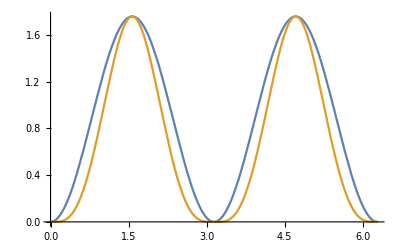

```mathematica
evParam={E1->-Log[p],E0->-Log[1-p]}/.p->0.1;
compareDiag=Plot[{Sρσ/.evParam,SρDσ/.evParam},{θ,0,2π}]
```

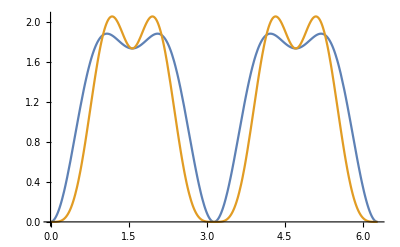

```mathematica
evParam={E1->-Log[p],E0->-Log[1-p]}/.p->0.1;
compareDiag=Plot[{Vρσ/.evParam,VρDσ/.evParam},{θ,0,2π}]
```

### Implementation

This section contains the functions that implement the measurement protocols. It should be executed before the next section “Results”.

```mathematica
SetOptions[$FrontEndSession,EvaluationCompletionAction->"ShowTiming"]

(*We set 0^0=1 to obtain a consistent dot product for θ=π/2*)
Unprotect[Power];
Power[0|0.,0|0.]=1;
Protect[Power];

(*The global variables are: NN, σEV, ρEV, ξHat, naccOpt, naccSimp, basis, zeroVec, θglobal.
The values for the relative entropy and the relative entropy variance used here are computed above.*)
Init[p_,θ_,ϵ_,Eoptval_:-∞,precomp_:True]:=Module[{σ,ρ,E1,E0,Sρσ,Vρσ,SρDσ,VρDσ,Eopt=Eoptval,Esimp},
{E1,E0}={-Log[p],-Log[1-p]};
Print["N=", NN, " | p=",p," | θ=", θ," | ϵ=",ϵ," | E_1=",E1," | E_0=",E0];

σ=({{ⅇ^-E0, 0}, {0, ⅇ^-E1}})//N;
ρ=({{ⅇ^-E0 Cos[θ]^2+ⅇ^-E1 Sin[θ]^2, (-ⅇ^-E0+ⅇ^-E1) Cos[θ] Sin[θ]}, {(-ⅇ^-E0+ⅇ^-E1) Cos[θ] Sin[θ], ⅇ^-E1 Cos[θ]^2+ⅇ^-E0 Sin[θ]^2}})//N;
θglobal=θ;

basis=Tuples[{0,1},NN];
zeroVec=ConstantArray[0,2^NN];

Sρσ=-(-1+2 p) Log[-1+1/p] Sin[θ]^2;
Vρσ=1/2 (1+4 p-4 p^2+(1-2 p)^2 Cos[2 θ]) Log[-1+1/p]^2 Sin[θ]^2;
SρDσ=1/2 ((-1+2 p) Cos[2 θ] Log[((-1+p) (1+(-1+2 p) Cos[2 θ]))/(p (-1+(-1+2 p) Cos[2 θ]))]-Log[(4 (-1+p) p)/(-1+(1-2 p)^2 Cos[2 θ]^2)]);
VρDσ=1/4 (-2 (-1+(-1+2 p) Cos[2 θ]) Log[(2 (-1+p))/(-1+(-1+2 p) Cos[2 θ])]^2+2 (1+(-1+2 p) Cos[2 θ]) Log[(2 p)/(1+(-1+2 p) Cos[2 θ])]^2-((-1+2 p) Cos[2 θ] Log[((-1+p) (1+(-1+2 p) Cos[2 θ]))/(p (-1+(-1+2 p) Cos[2 θ]))]+Log[(-1+(1-2 p)^2 Cos[2 θ]^2)/(4 (-1+p) p)])^2);
If[Eopt==-∞,Eopt=Sρσ+√(Vρσ/NN)invΦ[ϵ]];
Esimp=SρDσ+√(VρDσ/NN)invΦ[ϵ];
naccOpt=NN Eopt/(E1-E0);
naccSimp=NN((Esimp-E0-Log[ⅇ^-E0 Cos[θ]^2+ⅇ^-E1 Sin[θ]^2])/(E1-E0+Log[ⅇ^-E1 Cos[θ]^2+ⅇ^-E0 Sin[θ]^2]-Log[ⅇ^-E0 Cos[θ]^2+ⅇ^-E1 Sin[θ]^2]));
Print["S(ρ||σ)=",Sρσ," | V(ρ||σ)=",Vρσ," || S(ρ_D||σ)=",SρDσ," | V(ρ_D||σ)=",VρDσ,"\n"];

If[precomp,Print["Precomputation for σ (",AbsoluteTiming[σEV=PrecomputeEV[σ];][[1]], ")"]];
If[precomp,Print["Precomputation for ρ (",AbsoluteTiming[ρEV=PrecomputeEV[ρ];][[1]], ")\n"]];
];

invΦ[ϵ_]=√2 InverseErf[-1+2 ϵ];

n1C[Evec_]:=Module[{},
Return[∑_(i=1)^NN Evec[[i]]];
];

n10C[E1vec_,E2vec_]:=Module[{},
Return[∑_(i=1)^NN E1vec[[i]](1-E2vec[[i]])];
];

DotEEt[Evec_,Etvec_]:=Module[{n10Cev,n01Cev},
n10Cev=n10C[Etvec,Evec];
n01Cev=n10C[Evec,Etvec];
Return[(-1)^n10Cev Cos[θglobal]^(NN-n01Cev-n10Cev)Sin[θglobal]^(n01Cev+n10Cev)];
];

ξvec[Etvec_]:=Module[{nstar,res},
nstar=n1C[Etvec]+ naccOpt;
res=zeroVec;
Do[
If[n1C[basis[[i]]]≥ nstar,
res[[i]]=DotEEt[basis[[i]],Etvec] ;
];
,{i,Length[basis]}];
Return[res];
];

ComputeξHat[]:=Module[{listξ,dimSimp,dimOpt},
Print["Generating list of ξ (",
AbsoluteTiming[listξ=Table[ξvec[basis[[i]]],{i,Length[basis]}]][[1]],")"];
Print["Applying Gram-Schmidt (", AbsoluteTiming[ξHat= Orthogonalize[N[listξ]]][[1]],")"];

dimSimp=dimHsimp[];
dimOpt=dimHopt[];

Print["dim(H)=",2^NN];
Print["n_*=",naccSimp];

Print["dim(H_simp)=",dimSimp];
Print["dim(H_opt)=",dimOpt,"\n"];

Return[{dimSimp,dimOpt}];
];

dimHsimp[]:=Module[{res},
res=0;
Do[
If[n1C[basis[[i]]]≥ naccSimp,
res++]
,{i,2^NN}];
Return[res];
];

dimHopt[]:=Module[{iNull},
iNull=1;
While[ξHat[[-iNull]]==zeroVec, iNull++];
Return[2^NN+1-iNull];
];

PrecomputeEV[ρ_]:=Module[{res},
res=TensorProduct[zeroVec,zeroVec];
Do[
res[[i,j]]=∏_(k=1)^NN ρ[[basis[[i,k]]+1,basis[[j,k]]+1]];
If[j>i,res[[j,i]]=res[[i,j]]];
,{i,2^NN},{j,i,2^NN}];
Return[res];
];

OptimalMes[ρEV_]:=Module[{},
Return[Tr[ξHat.ρEV.Transpose[ξHat]]];
];

SimpMes[ρEV_]:=Module[{res},
res=0;
Do[
If[n1C[basis[[i]]]≥ naccSimp,
res+=ρEV[[i,i]]]
,{i,2^NN}];
Return[res];
];

Optimalβα[]:=Module[{βopt,αopt,βt,αt},
βt=Timing[βopt=OptimalMes[σEV]][[1]];
Print["β_opt=",βopt," (",βt,")"];
αt=Timing[αopt=1-OptimalMes[ρEV]][[1]];
Print["α_opt=",αopt," (",αt,")\n"];
Return[{βopt,αopt}];
];

Simpβα[]:=Module[{βsimp,αsimp,βt,αt},
βt=Timing[βsimp=SimpMes[σEV]][[1]];
Print["β_simp=",βsimp," (",βt,")"];
αt=Timing[αsimp=1-SimpMes[ρEV]][[1]];
Print["α_simp=",αsimp," (",αt,")\n"];
Return[{βsimp,αsimp}];
];
```

### Results

We now compare the optimal measurement with the likelihood ratio test. The above procedure implements these measurements. It computes the corresponding errors for n ranging from Nmin and Nmax. The results are printed and saved into “data”, which is used to plot them. 

We compute both types of errors: (αopt,βopt) for the optimal measurement and (αsimp,βsimp) for the likelihood ratio test. We also compare the dimensions dimOpt and dimpSimp of the respective acceptance subspaces. nacc_simp is the (not rounded) acceptance threshold n_* for the likelihood ratio test.

Note: the Gram-Schmidt algorithm is known to be unstable (due to small rounding errors) so the results below need to be taken cautiously.

```mathematica
data={};

Nmin=6;Nmax=13;
Do[NN=k;

(*Parameters:p,θ,ϵ*)
Init[0.015,π/3,0.2];

{dimSimp,dimOpt}=ComputeξHat[];
{βsimp,αsimp}=Simpβα[];
{βopt,αopt}=Optimalβα[];

AppendTo[data,{NN, {dimSimp,dimOpt},{βsimp,αsimp},{βopt,αopt}}];,{k,Nmin,Nmax}]
```

N=6 | p=0.015 | θ=π/3 | ϵ=0.2 | E_1=4.19971 | E_0=0.0151136

S(ρ||σ)=3.04429 | V(ρ||σ)=3.8654 || S(ρ_D||σ)=2.55175 | V(ρ_D||σ)=5.25693

Precomputation for σ (0.262511)

Precomputation for ρ (0.361888)

Generating list of ξ (0.037672)

Applying Gram-Schmidt (0.00585)

dim(H)=64

n_*=3.55358

dim(H_simp)=22

dim(H_opt)=33

β_simp=7.41264×10^-7 (0.000494)

α_simp=0.181474 (0.000559)

β_opt=5.36169×10^-8 (0.000226)

α_opt=0.2119 (0.000075)

N=7 | p=0.015 | θ=π/3 | ϵ=0.2 | E_1=4.19971 | E_0=0.0151136

S(ρ||σ)=3.04429 | V(ρ||σ)=3.8654 || S(ρ_D||σ)=2.55175 | V(ρ_D||σ)=5.25693

Precomputation for σ (0.195097)

Precomputation for ρ (0.178346)

Generating list of ξ (0.14438)

Applying Gram-Schmidt (0.001335)

dim(H)=128

n_*=4.22385

dim(H_simp)=29

dim(H_opt)=65

β_simp=1.55508×10^-8 (0.001176)

α_simp=0.259315 (0.001016)

β_opt=8.15474×10^-10 (0.001357)

α_opt=0.293112 (0.001256)

N=8 | p=0.015 | θ=π/3 | ϵ=0.2 | E_1=4.19971 | E_0=0.0151136

S(ρ||σ)=3.04429 | V(ρ||σ)=3.8654 || S(ρ_D||σ)=2.55175 | V(ρ_D||σ)=5.25693

Precomputation for σ (0.772142)

Precomputation for ρ (0.72007)

Generating list of ξ (0.615211)

Applying Gram-Schmidt (0.008235)

dim(H)=256

n_*=4.89913

dim(H_simp)=93

dim(H_opt)=129

β_simp=4.09507×10^-8 (0.002537)

α_simp=0.124456 (0.002493)

β_opt=3.75625×10^-10 (0.006901)

α_opt=0.598433 (0.00771)

N=9 | p=0.015 | θ=π/3 | ϵ=0.2 | E_1=4.19971 | E_0=0.0151136

S(ρ||σ)=3.04429 | V(ρ||σ)=3.8654 || S(ρ_D||σ)=2.55175 | V(ρ_D||σ)=5.25693

Precomputation for σ (3.09212)

Precomputation for ρ (3.18603)

Generating list of ξ (2.55944)

Applying Gram-Schmidt (0.048352)

dim(H)=512

n_*=5.57849

dim(H_simp)=130

dim(H_opt)=258

β_simp=9.20389×10^-10 (0.005043)

α_simp=0.180018 (0.004805)

β_opt=1.24004×10^-11 (0.038384)

α_opt=0.216723 (0.041488)

N=10 | p=0.015 | θ=π/3 | ϵ=0.2 | E_1=4.19971 | E_0=0.0151136

S(ρ||σ)=3.04429 | V(ρ||σ)=3.8654 || S(ρ_D||σ)=2.55175 | V(ρ_D||σ)=5.25693

Precomputation for σ (13.2146)

Precomputation for ρ (12.8579)

Generating list of ξ (10.1867)

Applying Gram-Schmidt (0.38911)

dim(H)=1024

n_*=6.26127

dim(H_simp)=176

dim(H_opt)=514

β_simp=1.97065×10^-11 (0.010228)

α_simp=0.2419 (0.010079)

β_opt=1.88531×10^-13 (0.231326)

α_opt=0.282451 (0.233872)

N=11 | p=0.015 | θ=π/3 | ϵ=0.2 | E_1=4.19971 | E_0=0.0151136

S(ρ||σ)=3.04429 | V(ρ||σ)=3.8654 || S(ρ_D||σ)=2.55175 | V(ρ_D||σ)=5.25693

Precomputation for σ (57.5479)

Precomputation for ρ (56.7554)

Generating list of ξ (42.8042)

Applying Gram-Schmidt (3.93894)

dim(H)=2048

n_*=6.94697

dim(H_simp)=562

dim(H_opt)=1537

β_simp=5.34821×10^-11 (0.021322)

α_simp=0.127031 (0.021127)

β_opt=1.89836×10^-13 (1.16182)

α_opt=0.162928 (1.51345)

N=12 | p=0.015 | θ=π/3 | ϵ=0.2 | E_1=4.19971 | E_0=0.0151136

S(ρ||σ)=3.04429 | V(ρ||σ)=3.8654 || S(ρ_D||σ)=2.55175 | V(ρ_D||σ)=5.25693

Precomputation for σ (242.682)

Precomputation for ρ (242.469)

Generating list of ξ (173.732)

Applying Gram-Schmidt (31.308)

dim(H)=4096

n_*=7.63519

dim(H_simp)=794

dim(H_opt)=3073

β_simp=1.20233×10^-12 (0.209499)

α_simp=0.173512 (0.211781)

β_opt=1.4961×10^-15 (10.267)

α_opt=0.584613 (10.5266)

N=13 | p=0.015 | θ=π/3 | ϵ=0.2 | E_1=4.19971 | E_0=0.0151136

S(ρ||σ)=3.04429 | V(ρ||σ)=3.8654 || S(ρ_D||σ)=2.55175 | V(ρ_D||σ)=5.25693

Precomputation for σ (1027.11)

Precomputation for ρ (1021.47)

Generating list of ξ (713.733)

Applying Gram-Schmidt (270.113)

dim(H)=8192

n_*=8.32564

dim(H_simp)=1093

dim(H_opt)=6145

β_simp=2.60328×10^-14 (0.090805)

α_simp=0.22528 (0.091076)

β_opt=4.40085×10^-17 (74.5981)

α_opt=0.270885 (75.6102)

We generate the plotting data and perform the plots. We first plot the type II error β.

```mathematica
Plotβopt=Table[{data[[i,1]],data[[i,4,1]]},{i,Length[data]}];
Plotβsimp=Table[{data[[i,1]],data[[i,3,1]]},{i,Length[data]}];
```

```mathematica
plotβopt=ListLogPlot[Plotβopt,Joined->True,Mesh->All,PlotLegends->SwatchLegend[{"Optimal measurement"},LegendMarkers->"Bubble"],MeshStyle->RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333],PlotStyle->RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333]];
plotβsimp=ListLogPlot[Plotβsimp,Joined->True,Mesh->All,PlotLegends->SwatchLegend[{"Likelihood ratio test"},LegendMarkers->"Bubble"],MeshStyle->RGBColor[0.9372549019607843, 0.7764705882352941, 0.],PlotStyle->RGBColor[0.9372549019607843, 0.7764705882352941, 0.]];
```

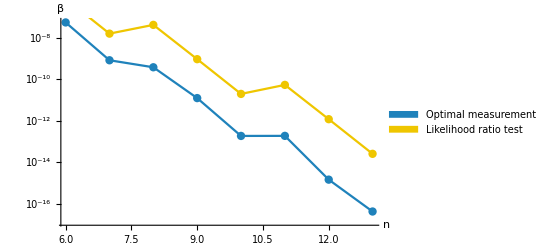

```mathematica
Show[plotβopt,plotβsimp,AxesLabel->{HoldForm[n],HoldForm[β]}]
```

We plot the type I error α.

```mathematica
Plotαopt=Table[{data[[i,1]],data[[i,4,2]]},{i,Length[data]}];
Plotαsimp=Table[{data[[i,1]],data[[i,3,2]]},{i,Length[data]}];
```

```mathematica
plotαopt=ListPlot[Plotαopt,Joined->True,Mesh->All,PlotLegends->SwatchLegend[{"Optimal measurement"},LegendMarkers->"Bubble"],MeshStyle->RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333],PlotStyle->RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333]];
plotαsimp=ListPlot[Plotαsimp,Joined->True,Mesh->All,PlotLegends->SwatchLegend[{"Likelihood ratio test"},LegendMarkers->"Bubble"],MeshStyle->RGBColor[0.9372549019607843, 0.7764705882352941, 0.],PlotStyle->RGBColor[0.9372549019607843, 0.7764705882352941, 0.]];
```

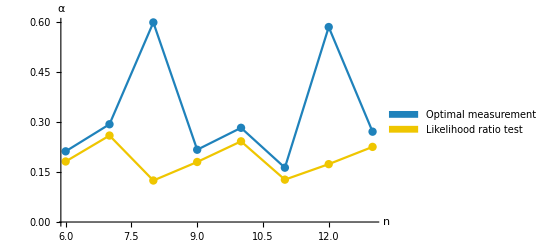

```mathematica
Show[plotαopt,plotαsimp,AxesLabel->{HoldForm[n],HoldForm[α]}]
```

We plot the dimensions of the acceptance subspaces.

```mathematica
PlotDimSimp=Table[{data[[i,1]],data[[i,2,1]]/2^data[[i,1]]},{i,Length[data]}];PlotDimOpt=Table[{data[[i,1]],data[[i,2,2]]/2^data[[i,1]]},{i,Length[data]}];
```

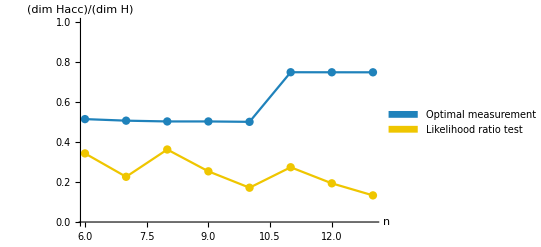

```mathematica
plotDimOpt=ListPlot[PlotDimOpt,Joined->True,Mesh->All,PlotLegends->SwatchLegend[{"Optimal measurement"},LegendMarkers->"Bubble"],MeshStyle->{RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333]},PlotStyle->RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333],PlotRange->{0,1}];
plotDimSimp=ListPlot[PlotDimSimp,Joined->True,Mesh->All,PlotLegends->SwatchLegend[{"Likelihood ratio test"},LegendMarkers->"Bubble"],MeshStyle->{RGBColor[0.9372549019607843, 0.7764705882352941, 0.]},PlotStyle->RGBColor[0.9372549019607843, 0.7764705882352941, 0.],PlotRange->{0,1}];

Show[plotDimOpt,plotDimSimp,AxesLabel->{HoldForm[n],HoldForm[(dim Hacc)/(dim H)]}]
```

We plot the “complexity” as defined from the minimal dimension between the acceptance subspace and its complement.

```mathematica
PlotCompSimp=Table[{data[[i,1]],Log[data[[i,2,1]]]},{i,Length[data]}];PlotCompOpt=Table[{data[[i,1]],Log[2^data[[i,1]]-data[[i,2,2]]]},{i,Length[data]}];
```

```mathematica
plotCompOpt=ListPlot[PlotCompOpt,Joined->True,Mesh->All,PlotLegends->SwatchLegend[{"Optimal measurement"},LegendMarkers->"Bubble"],MeshStyle->{RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333]},PlotStyle->RGBColor[0.12156862745098039, 0.5098039215686274, 0.7333333333333333],PlotRange->{0,10}];
plotCompSimp=ListPlot[PlotCompSimp,Joined->True,Mesh->All,PlotLegends->SwatchLegend[{"Likelihood ratio test"},LegendMarkers->"Bubble"],MeshStyle->{RGBColor[0.9372549019607843, 0.7764705882352941, 0.]},PlotStyle->RGBColor[0.9372549019607843, 0.7764705882352941, 0.],PlotRange->{0,10}];
```

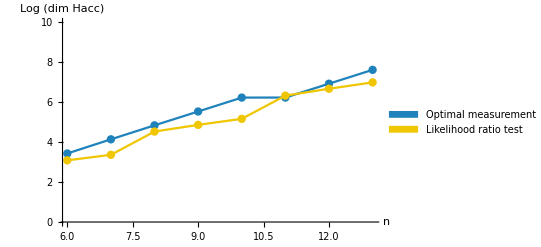

```mathematica
Show[plotCompOpt,plotCompSimp,AxesLabel->{HoldForm[n],HoldForm[Log (dim Hacc)]}]
```